Define our payoff functions with a parameter ω for mismatch extraction to be defined by the mutant’s value of alpha:

```mathematica
ClearAll[d]
(* v = specialist 1 frequency, p = specialist 2 frequency, m = mutant specialist 1, frequency Α = alpha, δ = alpha_g s = specialist carbon sharing, g = generalist carbon sharing *)
S1 = v*s*(1−Α)+m*s*(1−Α-d)+p*s*(1−α)+(1−v-m−p)*g*(1−δ);
S2 = (v)*s*(1-α)+(m)*s*(1−(ω))+p*s*(1−Α)+(1−v-m−p)*g*(1−δ);
S = u*(1-u)*(S1-S2);
S = Simplify[S]
H1=s*u*(Α−1)+(1−u)*s*(α−1);
HM = s*u*((Α+d)−1)+(1−u)*s*(ω)−1;
H2 = s*u*(α−1)+(1−u)*s*(Α−1);
HG =g*(δ−1);
Hbar = v*H1+p*H2+(1-v-p-m)(HG)+m*HM;
V=v(H1-Hbar);
V=Simplify[V]
P = p(H2-Hbar);
P = Simplify[P]
M = m(HM-Hbar);
M = Simplify[M]
```

s (-1+u) u (d m-v α+p (α-Α)+m Α+v Α-m ω)

v (m+s (-p (-1+u (α-Α)+Α)+(-1+v) (1+(-1+u) α-u Α))+g (-1+m+p+v) (-1+δ)-m s (u (-1+d+Α-ω)+ω))

p (m+s (-1+v+u α-v α+u v α+Α-u Α-u v Α-p (-1+u α+Α-u Α))+g (-1+m+p+v) (-1+δ)-m s (u (-1+d+Α-ω)+ω))

m (-1+m+s u (-1+d+Α)-p s (-1+u (α-Α)+Α)+s v (1+(-1+u) α-u Α)+g (-1+m+p+v) (-1+δ)-s (-1+u) ω-m s (u (-1+d+Α-ω)+ω))

change our variables and def

to make solving the system easier change to an explicit function of t, and define a litear tradeoff for alpha. Note that for mutants ω goes to (1-Α-d) in the linear tradeoff. d being the degree of change.

```mathematica
ClearAll[d]
d=0.01
{z'[t]==s (-1+u) u (d m-v α+p (α-Α)+m Α+v Α-m ω),
a'[t]==v (m+s (-p (-1+u (α-Α)+Α)+(-1+v) (1+(-1+u) α-u Α))+g (-1+m+p+v) (-1+δ)-m s (u (-1+d+Α-ω)+ω)),
b'[t]==p (m+s (-1+v+u α-v α+u v α+Α-u Α-u v Α-p (-1+u α+Α-u Α))+g (-1+m+p+v) (-1+δ)-m s (u (-1+d+Α-ω)+ω)),
c'[t]==m (-1+m+s u (-1+d+Α)-p s (-1+u (α-Α)+Α)+s v (1+(-1+u) α-u Α)+g (-1+m+p+v) (-1+δ)-s (-1+u) ω-m s (u (-1+d+Α-ω)+ω)),
b[0]==0.25,z[0]==0.25,a[0]==0.28-c[0],c[0]==0}//.{u-> z[t],v-> a[t],p-> b[t],m-> c[t], α-> (1-Α),ω -> (1-Α-d)};
```

Next I’ll copy over the resulting expressions to an explicit function - not the smoothest solution but it’s the one that worked:

0.01

```mathematica
System7[Α_,δ_, g_, s_]:= {z'[t]==s (-(1-Α) a[t]+Α a[t]+(1-2 Α) b[t]+0.1 c[t]-(0.9-Α) c[t]+Α c[t]) (-1+z[t]) z[t],a'[t]==a[t] (c[t]+g (-1+δ) (-1+a[t]+b[t]+c[t])-s c[t] (0.9-Α+(-1.8+2 Α) z[t])+s (-b[t] (-1+Α+(1-2 Α) z[t])+(-1+a[t]) (1+(1-Α) (-1+z[t])-Α z[t]))),b'[t]==b[t] (c[t]+g (-1+δ) (-1+a[t]+b[t]+c[t])-s c[t] (0.9-Α+(-1.8+2 Α) z[t])+s (-1+Α+a[t]-(1-Α) a[t]+(1-Α) z[t]-Α z[t]+(1-Α) a[t] z[t]-Α a[t] z[t]-b[t] (-1+Α+(1-Α) z[t]-Α z[t]))),c'[t]==c[t] (-1+c[t]+g (-1+δ) (-1+a[t]+b[t]+c[t])-s (0.9-Α) (-1+z[t])+s (-0.9+Α) z[t]-s b[t] (-1+Α+(1-2 Α) z[t])+s a[t] (1+(1-Α) (-1+z[t])-Α z[t])-s c[t] (0.9-Α+(-1.8+2 Α) z[t])),b[0]==0.25,z[0]==0.25,a[0]==0.28-c[0],c[0]==0}
```

The rest from here on out is the same as my previous methodology:

```mathematica
num7=System7[0.7,0.5,0.5,0.5];
Ans7=NDSolve[num7,{z,a,b,c},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
zstop=z[1000]/.Ans7;
astop=a[1000] /.Ans7;
bstop=b[1000 ] /.Ans7;
cstop=c[1000]/.Ans7;
```

```mathematica
Systeee[Α_,δ_, g_, s_]:= {z'[t]==s (-(1-Α) a[t]+Α a[t]+(1-2 Α) b[t]+0.1 c[t]-(0.9-Α) c[t]+Α c[t]) (-1+z[t]) z[t],a'[t]==a[t] (c[t]+g (-1+δ) (-1+a[t]+b[t]+c[t])-s c[t] (0.9-Α+(-1.8+2 Α) z[t])+s (-b[t] (-1+Α+(1-2 Α) z[t])+(-1+a[t]) (1+(1-Α) (-1+z[t])-Α z[t]))),b'[t]==b[t] (c[t]+g (-1+δ) (-1+a[t]+b[t]+c[t])-s c[t] (0.9-Α+(-1.8+2 Α) z[t])+s (-1+Α+a[t]-(1-Α) a[t]+(1-Α) z[t]-Α z[t]+(1-Α) a[t] z[t]-Α a[t] z[t]-b[t] (-1+Α+(1-Α) z[t]-Α z[t]))),c'[t]==c[t] (-1+c[t]+g (-1+δ) (-1+a[t]+b[t]+c[t])-s (0.9-Α) (-1+z[t])+s (-0.9+Α) z[t]-s b[t] (-1+Α+(1-2 Α) z[t])+s a[t] (1+(1-Α) (-1+z[t])-Α z[t])-s c[t] (0.9-Α+(-1.8+2 Α) z[t])),b[0]==bstop,z[0]==zstop,a[0]==astop-c[0],c[0]==0.05}
```

```mathematica
numeee=Systeee[0.7,0.5,0.5,0.5];
Ans=NDSolve[numeee,{z,a,b,c},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{zans,aans,bans,cans}= {z[t],a[t],b[t],c[t]} /.Flatten[Ans];
```

Join::heads: Heads List and InterpolatingFunction[{{0.,3000.}},{5,3,1,{5261},{4},0,0,0,0,Automatic,{},{},False},{{«1»}},{{{0.261753},{-0.00596324}},{{0.261752},{-0.00596296}},{{0.261752},{-0.00596268}},«46»,{{0.253393},{-0.00133691}},«5211»},{Automatic}] at positions 1 and 2 are expected to be the same.

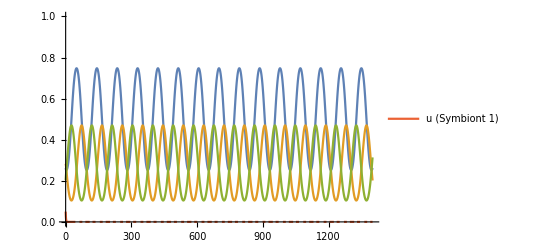

```mathematica
Plot[{zans,aans,bans,cans},{t,0,1400}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1"}]]
```